```mathematica
Au=0.0;
Bu=0.5;
αu=0.3;
αu'=0.45;
nu=4.83;
βu=4;
ETPFu[x_]:=(Bu+αu'Log[1./x]);
ETFLu[x_]:=nu*x^-αu*(1.-x)^βu;


Ad=0.0;
Bd=0.5;
αd=0.3;
αd'=0.45;
nd=3.57;
βd=5;
ETPFd[x_]:=(Bd+αd'Log[1./x]);
ETFLd[x_]:=nd*x^-αd*(1.-x)^βd;

ETu[x_,t_]:=ETFLu[x]*Exp[ETPFu[x]*t];
ETd[x_,t_]:=ETFLd[x]*Exp[ETPFd[x]*t];
```

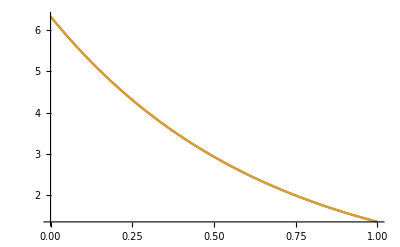

```mathematica
xx=0.1; tt=-0.1;
Plot[{ETu[xx,-t],EbarTu[xx,0.,-t]},{t,0,1}]
```